```mathematica
Get["https://raw.githubusercontent.com/srossd/SCWIGE/main/Install.m"]
```

```mathematica
<<SCWIGE`
```

"" | "" | "Setup Wizard" | "Editing: " | 
"" | "" | "Signature: " | 
"Defect: " |  |  | 
"" | "" |  | "" | ""
"" | "" |  | "Add Multiplet" |

## 𝒩 = 2 Defect

```mathematica
SetRSymmetry[{SU2,U1}];
SetDefectRSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[3];
```

### Vector multiplet

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[\"φ\", TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{{0},2},2,{1,0},2]},{Operator["\!\(\*FormBox[OverscriptBox[\"φ\", \"_\"], TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-1},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{{0},-2},2,{0,1},-2]}},"Vector",False,1]
```

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,3];
```

```mathematica
DisplaySUSYVariations[]
```

1

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,2];
```

```mathematica
Do[SetTwoPtRInvariant[rep,ConjugateIrrep[RSymmetry[],rep],SparseArray@IdentityMatrix[Times@@DimR[RSymmetry[],rep]]],{rep,RRep/@Multiplet[2]}]
SetTwoPtRInvariant[{0},{0},SparseArray@IdentityMatrix[1]];
SetTwoPtRInvariant[{2},{2},SparseArray@IdentityMatrix[3]]
SetTwoPtRInvariant[{1},{1},LeviCivitaTensor[2]]
SetTwoPtRInvariant[{1},AlternateRep[{1}],IdentityMatrix[2]]
SetTwoPtRInvariant[AlternateRep[{1}],AlternateRep[{1}],LeviCivitaTensor[2]]
```

```mathematica
SetThreePtRInvariant[{{2},0},{{1},1},{{1},-1},SparseArray[(PauliMatrix/@Range[3])]]
SetThreePtRInvariant[{{0},-2},{{1},1},{{1},1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtRInvariant[{{0},2},{{1},-1},{{1},-1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtRInvariant[{{0},0},{{1},1},{{1},-1},SparseArray[{IdentityMatrix[2]}]]

SetThreePtRInvariant[{2},{1},{1},SparseArray[(PauliMatrix[#].LeviCivitaTensor[2])&/@Range[3]]]
SetThreePtRInvariant[{2},{1},AlternateRep[{1}],SparseArray[(PauliMatrix[#])&/@Range[3]]]
SetThreePtRInvariant[{2},AlternateRep[{1}],AlternateRep[{1}],SparseArray[(LeviCivitaTensor[2].PauliMatrix[#])&/@Range[3]]]
SetThreePtRInvariant[{0},{1},{1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtRInvariant[{0},{1},AlternateRep[{1}],SparseArray[{IdentityMatrix[2]}]]
SetThreePtRInvariant[{0},AlternateRep[{1}],AlternateRep[{1}],SparseArray[{LeviCivitaTensor[2]}]]
```

Cached spacetime structure data (saves about 10 minutes):

```mathematica
Get["rel_data.mx"];
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Sign testing

```mathematica
pairs={{"ϕ","χ"},{"ϕ","χ̄"},{"χ","Σ"},{"χ","Σ̄"},{"χ̄","Σ"},{"χ̄","Σ̄"}};
Clear[eqExpr];
eqExpr[pair_]:=eqExpr[pair]=ExpandCorrelator@Correlator[NormalOrder[TensorProduct[QTensor[]+Contract[TensorProduct[TwoPtRInvariant[{2,1},{2,1}],σLowerSingle[4],ϵUpperDot,QTensor["QBar"->True]],{{2,7},{4,5},{6,8}}],Tensor[pair]],"Vacuum"->True],"Defect"->True];
signs[pair_]:=Module[{expr,structs},
expr=eqExpr[pair];
structs=DeleteDuplicates[{RPart[#],First@Cases[#,g[fields_,_,_]:>fields[[;;,1]],All,Heads->True]}&/@(List@@expr)];
Table[Labeled[Style[UndirectedEdge[pair,s[[2]]],If[ArrayRules[Flatten[Normal[CanonicallyOrderedComponents[s[[1]]]]]][[1,2]]>0,Black,Orange]],Style[s[[1]],Background->White]],{s,structs}]
]
```

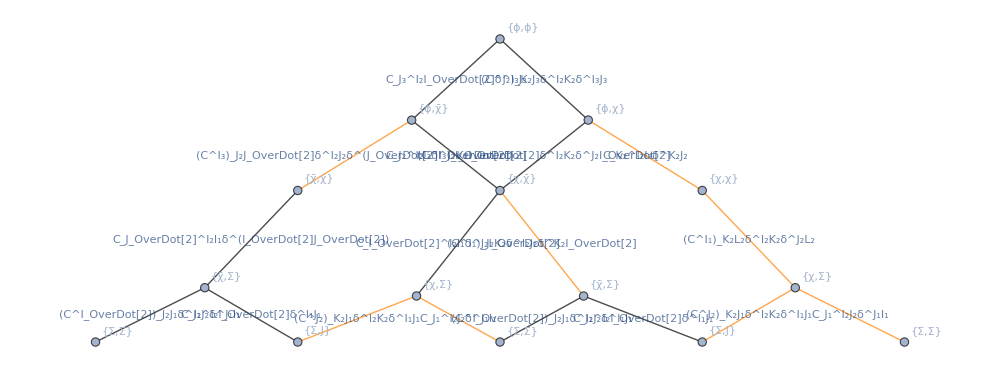

```mathematica
EdgeTaggedGraph[Join@@(signs/@pairs),VertexLabels->Automatic,VertexCoordinates->Thread[Tuples[Multiplet[2][[;;,1]],2]->({2(Last[#[[1]]]+Last[#[[2]]]),-3(ScalingDimension[#[[1]]]+ScalingDimension[#[[2]]])}&/@Tuples[Multiplet[2],2])],ImageSize->1000]
```

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True]]
AddSolutions[SolveWard[{"χ","Σ"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","Σ̄"},"Defect"->True]]
```

```mathematica
DumpSave["rel_data.mx",SCWIGE`Private`spacetimePtData]
```

{SCWIGE`Private`spacetimePtData}

```mathematica
tt=Exp[-2I φ]g[Multiplet[2][[{6,6}]],1,1][u,v]+2g[Multiplet[2][[{5,6}]],1,1][u,v]+Exp[2I φ]g[Multiplet[2][[{5,5}]],1,1][u,v]
```

ⅇ^(-2 ⅈ φ) g_11^(Σ̄Σ̄)(u,v)+2 g_11^(ΣΣ̄)(u,v)+ⅇ^(2 ⅈ φ) g_11^ΣΣ(u,v)

```mathematica
hSolved=Collect[tt/.(First/@SolvedCorrelators[])/.g[Multiplet[2][[{1,1}]],1,1]->a,Derivative[__][a][__],FullSimplify]
%/.{u->U,v->V}//InputForm
```

1/4 a^(1,0)(u,v) (4 u^2-4 u (u+v) cos(2 φ)+6 u v+3 v^2-1)+1/4 a^(0,1)(u,v) ((2 u v-v^2+1) cos(2 φ)-2 u v-3 v^2+1)-1/4 (v^2-1) a^(0,2)(u,v) (u (-cos(2 φ))+u+v)+1/4 (v^2-1) a^(1,1)(u,v) (u (-cos(2 φ))+u+v)-1/4 u (u+v) a^(2,0)(u,v) (u cos(2 φ)-u-v)+1/2 a(u,v) (u-(u+v) cos(2 φ))

(a[U, V]*(U - (U + V)*Cos[2*φ]))/2 + ((1 - 2*U*V - 3*V^2 + (1 + 2*U*V - V^2)*Cos[2*φ])*Derivative[0, 1][a][U, V])/4 - 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[0, 2][a][U, V])/4 + ((-1 + 4*U^2 + 6*U*V + 3*V^2 - 4*U*(U + V)*Cos[2*φ])*Derivative[1, 0][a][U, V])/4 + 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[1, 1][a][U, V])/4 - (U*(U + V)*(-U - V + U*Cos[2*φ])*Derivative[2, 0][a][U, V])/4

```mathematica
Collect[hSolved/.φ->0,a[__]|Derivative[__][a][__],Simplify]
Collect[hSolved/.φ->Pi/2,a[__]|Derivative[__][a][__],Simplify]
```

(1/2-v^2) a^(0,1)(u,v)-1/4 v (v^2-1) a^(0,2)(u,v)+1/4 (2 u v+3 v^2-1) a^(1,0)(u,v)+1/4 v (v^2-1) a^(1,1)(u,v)+1/4 u v (u+v) a^(2,0)(u,v)-1/2 v a(u,v)

1/4 (8 u^2+10 u v+3 v^2-1) a^(1,0)(u,v)-1/4 (v^2-1) (2 u+v) a^(0,2)(u,v)+1/4 (v^2-1) (2 u+v) a^(1,1)(u,v)-1/2 v (2 u+v) a^(0,1)(u,v)+1/4 u (u+v) (2 u+v) a^(2,0)(u,v)+(u+v/2) a(u,v)

```mathematica
Table[{k->SolvedCorrelators[][k][[1]][u,v]/.g[Multiplet[2][[{1,1}]],1,1]->({u,v}|->1/(16 u^2))},{k,Keys[SolvedCorrelators[]]}]//Simplify
```

{{g_11^(χχ̄)→ⅈ/(64 u^3)},{g_12^(χχ̄)→0},{g_13^(χχ̄)→0},{g_14^(χχ̄)→0},{g_11^χχ→0},{g_12^χχ→0},{g_13^χχ→0},{g_14^χχ→0},{g_11^(χ̄χ̄)→0},{g_12^(χ̄χ̄)→0},{g_13^(χ̄χ̄)→0},{g_14^(χ̄χ̄)→0},{g_11^ΣJ→0},{g_12^ΣJ→0},{g_13^ΣJ→0},{g_14^ΣJ→0},{g_11^(ΣΣ̄)→1/(64 u^3)},{g_11^ΣΣ→0},{g_11^(Σ̄J)→0},{g_12^(Σ̄J)→0},{g_13^(Σ̄J)→0},{g_14^(Σ̄J)→0},{g_11^(Σ̄Σ̄)→0}}

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_11^(χχ̄)→{{u,v}↦1/8 ⅈ ((g_11^ϕϕ)^(0,1)(u,v)-(g_11^ϕϕ)^(1,0)(u,v))}
g_12^(χχ̄)→{{u,v}↦1/8 ⅈ v (2 g_11^ϕϕ(u,v)+v (g_11^ϕϕ)^(0,1)(u,v)+u (g_11^ϕϕ)^(1,0)(u,v))}
g_13^(χχ̄)→{{u,v}↦0}
g_14^(χχ̄)→{{u,v}↦0}
g_11^χχ→{{u,v}↦0}
g_12^χχ→{{u,v}↦0}
g_13^χχ→{{u,v}↦-1/8 ⅈ (g_11^ϕϕ)^(0,1)(u,v)}
g_14^χχ→{{u,v}↦-1/8 ⅈ v (2 g_11^ϕϕ(u,v)+v (g_11^ϕϕ)^(0,1)(u,v)+u (g_11^ϕϕ)^(1,0)(u,v))}
g_11^(χ̄χ̄)→{{u,v}↦0}
g_12^(χ̄χ̄)→{{u,v}↦0}
g_13^(χ̄χ̄)→{{u,v}↦1/8 ⅈ (g_11^ϕϕ)^(0,1)(u,v)}
g_14^(χ̄χ̄)→{{u,v}↦1/8 ⅈ v (2 g_11^ϕϕ(u,v)+v (g_11^ϕϕ)^(0,1)(u,v)+u (g_11^ϕϕ)^(1,0)(u,v))}
g_11^ΣJ→{{u,v}↦0}
g_12^ΣJ→{{u,v}↦0}
g_13^ΣJ→{{u,v}↦-(u^2 (g_11^ϕϕ)^(2,0)(u,v)+v^2 ((g_11^ϕϕ)^(1,1)(u,v)-(g_11^ϕϕ)^(0,2)(u,v))+4 u (g_11^ϕϕ)^(1,0)(u,v)+2 g_11^ϕϕ(u,v)+(g_11^ϕϕ)^(0,2)(u,v)-(g_11^ϕϕ)^(1,1)(u,v)+v (-2 (g_11^ϕϕ)^(0,1)(u,v)+3 (g_11^ϕϕ)^(1,0)(u,v)+u (g_11^ϕϕ)^(2,0)(u,v)))/(16 √6)}
g_14^ΣJ→{{u,v}↦(u^2 (g_11^ϕϕ)^(2,0)(u,v)+v^2 ((g_11^ϕϕ)^(1,1)(u,v)-(g_11^ϕϕ)^(0,2)(u,v))+2 u (g_11^ϕϕ)^(1,0)(u,v)-2 g_11^ϕϕ(u,v)+(g_11^ϕϕ)^(0,2)(u,v)-(g_11^ϕϕ)^(1,1)(u,v)+v (-4 (g_11^ϕϕ)^(0,1)(u,v)+3 (g_11^ϕϕ)^(1,0)(u,v)+u (g_11^ϕϕ)^(2,0)(u,v)))/(8 √6)}
g_11^(ΣΣ̄)→{{u,v}↦1/8 (u^3 (g_11^ϕϕ)^(2,0)(u,v)+4 u^2 (g_11^ϕϕ)^(1,0)(u,v)+2 u^2 v (g_11^ϕϕ)^(2,0)(u,v)-v^3 (g_11^ϕϕ)^(0,2)(u,v)+v^3 (g_11^ϕϕ)^(1,1)(u,v)-u v^2 (g_11^ϕϕ)^(0,2)(u,v)+u v^2 (g_11^ϕϕ)^(1,1)(u,v)+u v^2 (g_11^ϕϕ)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_11^ϕϕ)^(0,1)(u,v)+3 v^2 (g_11^ϕϕ)^(1,0)(u,v)+2 u g_11^ϕϕ(u,v)+u (g_11^ϕϕ)^(0,2)(u,v)+6 u v (g_11^ϕϕ)^(1,0)(u,v)-u (g_11^ϕϕ)^(1,1)(u,v)+v (g_11^ϕϕ)^(0,2)(u,v)-(g_11^ϕϕ)^(1,0)(u,v)-v (g_11^ϕϕ)^(1,1)(u,v))}
g_11^ΣΣ→{{u,v}↦1/8 (-u (u^2 (g_11^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_11^ϕϕ)^(0,2)(u,v)+v^2 (g_11^ϕϕ)^(1,1)(u,v)+u v (g_11^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_11^ϕϕ)^(1,0)(u,v)-(g_11^ϕϕ)^(1,1)(u,v))+(2 u v-v^2+1) (g_11^ϕϕ)^(0,1)(u,v)-2 (u+v) g_11^ϕϕ(u,v))}
g_11^(Σ̄J)→{{u,v}↦0}
g_12^(Σ̄J)→{{u,v}↦0}
g_13^(Σ̄J)→{{u,v}↦(u^2 (g_11^ϕϕ)^(2,0)(u,v)+v^2 ((g_11^ϕϕ)^(1,1)(u,v)-(g_11^ϕϕ)^(0,2)(u,v))+4 u (g_11^ϕϕ)^(1,0)(u,v)+2 g_11^ϕϕ(u,v)+(g_11^ϕϕ)^(0,2)(u,v)-(g_11^ϕϕ)^(1,1)(u,v)+v (-2 (g_11^ϕϕ)^(0,1)(u,v)+3 (g_11^ϕϕ)^(1,0)(u,v)+u (g_11^ϕϕ)^(2,0)(u,v)))/(16 √6)}
g_14^(Σ̄J)→{{u,v}↦(u^2 (g_11^ϕϕ)^(2,0)(u,v)+v^2 ((g_11^ϕϕ)^(1,1)(u,v)-(g_11^ϕϕ)^(0,2)(u,v))+2 u (g_11^ϕϕ)^(1,0)(u,v)-2 g_11^ϕϕ(u,v)+(g_11^ϕϕ)^(0,2)(u,v)-(g_11^ϕϕ)^(1,1)(u,v)+v (-4 (g_11^ϕϕ)^(0,1)(u,v)+3 (g_11^ϕϕ)^(1,0)(u,v)+u (g_11^ϕϕ)^(2,0)(u,v)))/(8 √6)}
g_11^(Σ̄Σ̄)→{{u,v}↦1/8 (-u (u^2 (g_11^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_11^ϕϕ)^(0,2)(u,v)+v^2 (g_11^ϕϕ)^(1,1)(u,v)+u v (g_11^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_11^ϕϕ)^(1,0)(u,v)-(g_11^ϕϕ)^(1,1)(u,v))+(2 u v-v^2+1) (g_11^ϕϕ)^(0,1)(u,v)-2 (u+v) g_11^ϕϕ(u,v))}

## 𝒩 = 2

```mathematica
SetRSymmetry[{SU2,U1}]
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Flavor",True,1];
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,2];
SetMultiplet[{Operator["\!\(\*FormBox[\"M\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"Z\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Z\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[\"j1\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"j2\", TraditionalForm]\)",{{2},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"κ\", TraditionalForm]\)",{{1},1},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ\", \"_\"], TraditionalForm]\)",{{1},-1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{{0},0},4,{1,1},0]},"Stress Tensor",True,3];
```

```mathematica
DisplaySUSYVariations[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

123

### Determine ⟨ϕϕϕϕ⟩

```mathematica
eqs=WardEquations[{"ϕ","ϕ","ϕ","χ̄"}]
```

{2 √2 v^3 g_12^(ϕϕχχ̄)(1/u,v/u)-2 √2 g_12^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_11^(ϕϕχχ̄)(1/u,v/u)+(√2 u g_11^(ϕϕχχ̄)(v/u,1/u))/v^2-√2 u (v+1) g_12^(ϕϕχχ̄)(1/u,v/u)-(ⅈ (g_21^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_31^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-(√2 g_11^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+√2 g_12^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ (g_21^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_31^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_11^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_11^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)-((-u+v+1) g_12^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-(ⅈ g_21^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_31^ϕϕϕϕ(u,v))/(√2)==0,-2 √2 g_12^(ϕϕχχ̄)(1/u,v/u) v^3-(2 √2 g_22^(ϕϕχχ̄)(u,v) v^3)/u^3==0,(ⅈ √(3/2) g_12^ϕϕϕJ(u,v))/u-√2 u g_11^(ϕϕχχ̄)(1/u,v/u)+√2 u (v+1) g_12^(ϕϕχχ̄)(1/u,v/u)+(√2 g_22^(ϕϕχχ̄)(u,v))/u^2+(ⅈ (g_21^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-√2 g_12^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ √(3/2) g_12^ϕϕϕJ(u,v))/v+(ⅈ (g_21^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ √(3/2) g_11^ϕϕϕJ(u,v))/(v u)==0,-(g_11^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+((-u+v+1) g_12^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_21^ϕϕϕϕ(u,v))/(√2)+(g_21^(ϕϕχχ̄)(u,v))/(√2)-((u-1) g_22^(ϕϕχχ̄)(u,v))/(√2 u)==0,(2 √2 g_12^(ϕϕχχ̄)(u,v) v^3)/u^3+2 √2 g_22^(ϕϕχχ̄)(1/u,v/u) v^3==0,-(ⅈ √(3/2) g_12^ϕϕϕJ(u,v))/u-(√2 g_12^(ϕϕχχ̄)(u,v))/u^2+√2 u g_21^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_22^(ϕϕχχ̄)(1/u,v/u)+(ⅈ (g_11^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_22^(ϕϕχχ̄)(1/u,v/u) u^2+(ⅈ √(3/2) g_12^ϕϕϕJ(u,v))/v+(ⅈ (g_11^ϕϕϕϕ)^(0,1)(u,v))/(√2)+(ⅈ √(3/2) g_11^ϕϕϕJ(u,v))/(v u)==0,(g_21^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_22^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_11^ϕϕϕϕ(u,v))/(√2)-(g_11^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_12^(ϕϕχχ̄)(u,v))/(√2 u)==0,2 √2 g_12^(ϕϕχχ̄)(1/u,v/u) v^3+(2 √2 g_12^(ϕϕχχ̄)(u,v) v^3)/u^3-2 √2 g_22^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_11^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_12^(ϕϕχχ̄)(1/u,v/u)-(√2 g_12^(ϕϕχχ̄)(u,v))/u^2+(√2 u g_21^(ϕϕχχ̄)(v/u,1/u))/v^2+(ⅈ (g_11^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_21^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_12^(ϕϕχχ̄)(1/u,v/u) u^2-(√2 g_21^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+(ⅈ (g_11^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_21^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_11^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_12^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_21^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)+(ⅈ g_11^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_21^ϕϕϕϕ(u,v))/(√2)-(g_11^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_12^(ϕϕχχ̄)(u,v))/(√2 u)==0}

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,3}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v]}]
```

{g_11^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(1)(u,v)),g_21^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(2)(u,v)),g_31^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(3)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_12^(ϕϕχχ̄)(1/u,v/u),g_12^(ϕϕχχ̄)(v/u,1/u),g_11^(ϕϕχχ̄)(1/u,v/u),g_11^(ϕϕχχ̄)(v/u,1/u),g_22^(ϕϕχχ̄)(u,v),g_12^ϕϕϕJ(u,v),g_11^ϕϕϕJ(u,v),g_21^(ϕϕχχ̄)(u,v),g_12^(ϕϕχχ̄)(u,v),g_22^(ϕϕχχ̄)(1/u,v/u),g_21^(ϕϕχχ̄)(1/u,v/u),g_11^(ϕϕχχ̄)(u,v),g_22^(ϕϕχχ̄)(v/u,1/u),g_21^(ϕϕχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify)
```

{1/(2 √2 u)ⅈ (u (u 𝒯^(0,1)(u,v) f(1)(u,v)+((u-v) 𝒯^(0,1)(u,v)+(u-v+1) 𝒯^(1,0)(u,v)) f(2)(u,v)-(v 𝒯^(0,1)(u,v)+(u+v-1) 𝒯^(1,0)(u,v)) f(3)(u,v))+𝒯(u,v) (-2 (u-v+1) f(2)(u,v)+2 (v-1) f(3)(u,v)+u (u (f(1))^(0,1)(u,v)+(u-v) (f(2))^(0,1)(u,v)-v (f(3))^(0,1)(u,v)+u (f(2))^(1,0)(u,v)-v (f(2))^(1,0)(u,v)+(f(2))^(1,0)(u,v)-u (f(3))^(1,0)(u,v)-v (f(3))^(1,0)(u,v)+(f(3))^(1,0)(u,v)))),1/(√2 u v)ⅈ (u ((𝒯^(0,1)(u,v)+𝒯^(1,0)(u,v)) (-f(2)(u,v))+(v 𝒯^(0,1)(u,v)+(u-1) 𝒯^(1,0)(u,v)) f(3)(u,v)+((v-1) 𝒯^(0,1)(u,v)+u 𝒯^(1,0)(u,v)) f(1)(u,v))+𝒯(u,v) (2 f(2)(u,v)+2 f(3)(u,v)+u ((v-1) (f(1))^(0,1)(u,v)-(f(2))^(0,1)(u,v)+v (f(3))^(0,1)(u,v)+u (f(1))^(1,0)(u,v)-(f(2))^(1,0)(u,v)+u (f(3))^(1,0)(u,v)-(f(3))^(1,0)(u,v))))}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform
```

{ⅈ (-2 (u-v+1) (α(2)+β(2) u+γ(2) v)+2 (v-1) (α(3)+β(3) u+γ(3) v)+u (β(2)+β(3)+β(2) u-β(3) u+γ(1) u+γ(2) (u-v)-β(2) v-β(3) v-γ(3) v))==0,ⅈ (2 (α(2)+β(2) u+γ(2) v)+2 (α(3)+β(3) u+γ(3) v)+u (-β(2)-β(3)-γ(2)+β(1) u+β(3) u+γ(1) (v-1)+γ(3) v))==0,ⅈ (u^2 (α(2)+β(2) u+γ(2) v)-u^2 (α(3)+β(3) u+γ(3) v)-u v (α(2)+β(2) u+γ(2) v)+u (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v)+u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(3)+β(3) u+γ(3) v)-u (α(2)+β(2) u+γ(2) v)-u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(2)+β(2) u+γ(2) v)-u v (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v))==0,ⅈ (-u (α(1)+β(1) u+γ(1) v)+u v (α(1)+β(1) u+γ(1) v)-u (α(2)+β(2) u+γ(2) v)+u v (α(3)+β(3) u+γ(3) v))==0}

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(2)→-α(1),α(3)→α(1),β(1)→-α(1),β(2)→α(1),β(3)→α(1),γ(1)→α(1),γ(2)→α(1),γ(3)→-α(1)}

```mathematica
Table[f[i][u,v],{i,3}]/.fform/.coeffSol/.α[1]->1
```

{-u+v+1,u+v-1,u-v+1}

### Find ,

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],(v/u)^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],u^-1 𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],u^-1 v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],u^-2 v 𝒯[u,v]];
```

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,3}]->{(1-u+v) 𝒯[u,v],(u+v-1)𝒯[u,v],(u-v+1)𝒯[u,v]}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","J","χ̄"}]];
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ","χ̄","Σ̄"}]];
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","Σ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ","Σ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","χ","Σ̄"}]];
```

### Find

```mathematica
DeclareArbitraryFunction[𝒫];
DeclareCrossingRule[𝒫[v,u],𝒫[v,u]];
DeclareCrossingRule[𝒫[u/v,1/v],𝒫[u,v]];
DeclareCrossingRule[𝒫[1/u,v/u],𝒫[1/u,v/u]];
DeclareCrossingRule[𝒫[v/u,1/u],𝒫[v,u]];
DeclareCrossingRule[𝒫[1/v,u/v],𝒫[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[1][[1]],Multiplet[1][[1]]},1,1][u,v]->𝒫[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ","Σ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ̄","Σ"},"QBar"->True]]
```

### Find , ,

```mathematica
DeclareArbitraryFunction[𝒲];
DeclareCrossingRule[𝒲[v,u],𝒲[v,u]];
DeclareCrossingRule[𝒲[u/v,1/v],𝒲[u,v]];
DeclareCrossingRule[𝒲[1/u,v/u],𝒲[1/u,v/u]];
DeclareCrossingRule[𝒲[v/u,1/u],𝒲[v,u]];
DeclareCrossingRule[𝒲[1/v,u/v],𝒲[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[3][[1]],Multiplet[3][[1]]},1,1][u,v]->𝒲[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","Z̄"}]]
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","Z"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j1"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","j1"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j2"}]]
```

```mathematica
Put[SolvedCorrelators[],"n2_correlators_test.m"]
```

## 𝒩 = 4 Vector

```mathematica
SetRSymmetry[SU4]
SetMultiplet[{Operator["\!\(\*FormBox[\"X\", TraditionalForm]\)",{0,1,0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,0,0},2,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,0,0},2,{0,1},-2]},"Vector",True,1];
```

```mathematica
DisplaySUSYVariations["Solved"->False]
```

1

## 𝒩 = 4 Stress tensor

```mathematica
SetRSymmetry[SU4];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
Get["C:/users/rossd/downloads/ThreePtStructures2.txt"];
Get["C:/users/rossd/downloads/FourPtStructures2.txt"];
```

```mathematica
SetTwoPtRInvariant[6,6,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6}]]];
SetTwoPtRInvariant[4,-4,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}]]];
SetTwoPtRInvariant[1,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,1},{j,1,1}]]];
SetTwoPtRInvariant[10,-10,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10}]]];
SetTwoPtRInvariant[15,15,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15}]]];
SetTwoPtRInvariant[20,-20,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
SetTwoPtRInvariant[{0,2,0},{0,2,0},SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
```

```mathematica
SetThreePtRInvariant[4,{0,2,0},-20,SparseArray[threeptinvt420p20b]];
SetThreePtRInvariant[4,20,10,SparseArray[threeptinvt42010]];
SetThreePtRInvariant[4,20,6,SparseArray[threeptinvt4206]];
SetThreePtRInvariant[4,6,4,SparseArray[threeptinvt464]];
SetThreePtRInvariant[4,-4,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4},{k,1,1}]]];
SetThreePtRInvariant[4,-20,15,SparseArray[Conjugate[threeptinvt4b2015]]];
SetThreePtRInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtRInvariant[4,-10,4,SparseArray[threeptinvt410b4]];
SetThreePtRInvariant[-4,{0,2,0},20,SparseArray[Conjugate[threeptinvt420p20b]]];
SetThreePtRInvariant[-4,-20,-10,SparseArray[Conjugate[threeptinvt42010]]];
SetThreePtRInvariant[-4,-20,-6,SparseArray[Conjugate[threeptinvt4206]]];
SetThreePtRInvariant[-4,6,-4,SparseArray[Conjugate[threeptinvt464]]];
SetThreePtRInvariant[-4,20,15,SparseArray[threeptinvt4b2015]];
SetThreePtRInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtRInvariant[-4,10,-4,SparseArray[Conjugate[threeptinvt410b4]]];
```

```mathematica
SetThreePtRInvariant[{0,2,0},6,6,SparseArray[threeptinvt20p66]];
SetThreePtRInvariant[15,6,6,SparseArray[threeptinvt1566]];
SetThreePtRInvariant[{0,2,0},{0,2,0},15,SparseArray[threeptinvt20p20p15]];
SetThreePtRInvariant[{0,2,0},15,15,SparseArray[threeptinvt20p1515]];
SetThreePtRInvariant[{0,2,0},{0,2,0},{0,2,0},SparseArray[threeptinvt20p20p20p]];
SetThreePtRInvariant[{0,2,0},{0,2,0},1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtRInvariant[20,-20,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtRInvariant[15,15,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15},{k,1,1}]]];
SetThreePtRInvariant[6,6,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6},{k,1,1}]]];
SetThreePtRInvariant[10,-10,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10},{k,1,1}]]];
SetThreePtRInvariant[{0,2,0},20,-20,SparseArray[threeptinvt20p2020b]];
SetThreePtRInvariant[{0,2,0},10,10,SparseArray[threeptinvt20p1010]];
SetThreePtRInvariant[{0,2,0},-10,-10,SparseArray[Conjugate[threeptinvt20p1010]]];
SetThreePtRInvariant[20,20,6,SparseArray[threeptinvt20206]];
SetThreePtRInvariant[-20,-20,6,SparseArray[Conjugate[threeptinvt20206]]];
SetThreePtRInvariant[20,20,10,SparseArray[threeptinvt202010]];
SetThreePtRInvariant[-20,-20,-10,SparseArray[Conjugate[threeptinvt202010]]];
SetThreePtRInvariant[10,-10,15,SparseArray[threeptinvt1010b15]];
SetThreePtRInvariant[6,10,15,SparseArray[threeptinvt61015]];
SetThreePtRInvariant[6,-10,15,SparseArray[Conjugate[threeptinvt61015]]];
```

```mathematica
SetThreePtRInvariant[20,20,-10,SparseArray[threeptinvt202010b]];
SetThreePtRInvariant[-20,-20,10,SparseArray[Conjugate@threeptinvt202010b]];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],v^2/u^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],v^2/u^2 𝒯[u,v]];
```

### Find

```mathematica
eqs=WardEquations[{"S","S","S","χ̄"}];
```

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_11^SSSS→({u,v}↦𝒯(u,v) f(1)(u,v)),g_21^SSSS→({u,v}↦𝒯(u,v) f(2)(u,v)),g_31^SSSS→({u,v}↦𝒯(u,v) f(3)(u,v)),g_41^SSSS→({u,v}↦𝒯(u,v) f(4)(u,v)),g_51^SSSS→({u,v}↦𝒯(u,v) f(5)(u,v)),g_61^SSSS→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_12^(SSχχ̄)(1/u,v/u),g_12^(SSχχ̄)(u,v),g_22^(SSχχ̄)(1/u,v/u),g_22^(SSχχ̄)(u,v),g_11^(SSχχ̄)(1/u,v/u),g_21^(SSχχ̄)(1/u,v/u),g_11^(SSχχ̄)(u,v),g_21^(SSχχ̄)(u,v),g_12^(SSχχ̄)(v/u,1/u),g_22^(SSχχ̄)(v/u,1/u),g_32^(SSχχ̄)(1/u,v/u),g_32^(SSχχ̄)(u,v),g_11^(SSχχ̄)(v/u,1/u),g_21^(SSχχ̄)(v/u,1/u),g_31^(SSχχ̄)(1/u,v/u),g_31^(SSχχ̄)(u,v),g_32^(SSχχ̄)(v/u,1/u),g_31^(SSχχ̄)(v/u,1/u),g_42^(SSχχ̄)(u,v),g_12^SSSJ(u,v),g_11^SSSJ(u,v),g_41^(SSχχ̄)(u,v),g_42^(SSχχ̄)(1/u,v/u),g_32^SSSJ(u,v),g_41^(SSχχ̄)(1/u,v/u),g_31^SSSJ(u,v),g_42^(SSχχ̄)(v/u,1/u),g_41^(SSχχ̄)(v/u,1/u),g_52^(SSχχ̄)(u,v),g_22^SSSJ(u,v),g_21^SSSJ(u,v),g_51^(SSχχ̄)(u,v),g_52^(SSχχ̄)(1/u,v/u),g_51^(SSχχ̄)(1/u,v/u),g_52^(SSχχ̄)(v/u,1/u),g_51^(SSχχ̄)(v/u,1/u),g_62^(SSχχ̄)(u,v),g_61^(SSχχ̄)(u,v),g_62^(SSχχ̄)(1/u,v/u),g_61^(SSχχ̄)(1/u,v/u),g_62^(SSχχ̄)(v/u,1/u),g_61^(SSχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify);
```

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ξ[i] v^2));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(1)→0,α(2)→0,α(3)→0,α(5)→0,α(6)→0,β(1)→0,β(2)→0,β(3)→16 α(4),β(4)→-α(4),β(5)→0,β(6)→-α(4),γ(1)→16 α(4),γ(2)→0,γ(3)→0,γ(4)→-α(4),γ(5)→-α(4),γ(6)→0,δ(1)→0,δ(2)→16 α(4),δ(3)→0,δ(4)→0,δ(5)→-α(4),δ(6)→-α(4),ζ(1)→0,ζ(2)→0,ζ(3)→0,ζ(4)→0,ζ(5)→0,ζ(6)→α(4),ξ(1)→0,ξ(2)→0,ξ(3)→0,ξ(4)→0,ξ(5)→α(4),ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.α[4]->1/16//Simplify
```

{v,u v,u,1/16 (-u-v+1),1/16 v (-u+v-1),1/16 u (u-v-1)}

### Solve identities

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,6}]->(multipliers 𝒯[u,v])]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","S","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F̄","χ"}]];
```

```mathematica
AbsoluteTiming[AddSolutions[SolveWard[{"S","S","χ̄","J"}]]]
```

{1280.56,Null}

```mathematica
repeats=Select[SolvedCorrelators[],Length[#]>1&];
Flatten@Table[FullSimplify[Differences@Table[ff[u,v],{ff,repeats[Keys[repeats][[i]]]}],u>0&&v>0],{i,Length[repeats]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Export["n4sym_correlators_lorentzian.m",First/@SolvedCorrelators[]]
```

n4sym_correlators_lorentzian.m

## Long

```mathematica
SetRSymmetry[SU4]
```

```mathematica
SetMultiplet[(<<"ward/long_multiplet.m"),"Long",True,1]
```

```mathematica
Simplify[#,Δ!=0&&_SUSYCoefficient != 0]&/@SCWIGE`Private`linearEquations[1,"MaxDepth"->2]
```

{Δ==(ⅈ 𝒶_(𝒪(0,0,1),1))/(2 𝒶_(𝒪(0,1,1),3)),Δ==(ⅈ (𝒶̄)_(𝒪(0,0,1),1))/(2 (𝒶̄)_(𝒪(1,0,1),3)),Δ==-(√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2)-ⅈ 𝒶_(𝒪(0,1,1),2))/(4 𝒶_(𝒪(1,1,1),3))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),2)+√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2))/(4 𝒶_(𝒪(1,1,1),3)),2 Δ+(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4))),Δ==-(√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2)-ⅈ 𝒶_(𝒪(0,1,1),1))/(4 𝒶_(𝒪(1,1,2),5))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),1)+√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2))/(4 𝒶_(𝒪(1,1,2),5)),2 Δ+(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6))),2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,Δ==(ⅈ (𝒶̄)_(𝒪(0,1,1),1))/(2 (𝒶̄)_(𝒪(2,0,2),4))+1,Δ==(ⅈ 𝒶_(𝒪(1,0,1),1))/(2 𝒶_(𝒪(0,2,1),4))+1,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),2))/(4 (𝒶̄)_(𝒪(1,1,1),3))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),2)+√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2))/(4 (𝒶̄)_(𝒪(1,1,1),3)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4))),Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),1))/(4 (𝒶̄)_(𝒪(1,1,2),5))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),1)+√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2))/(4 (𝒶̄)_(𝒪(1,1,2),5)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))}

```mathematica
SCWIGE`Private`quadraticEquations[1,"MaxDepth"->2]
```

{𝒶_(𝒪(0,0,1),1)==(2 ⅈ-(𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),3))/((𝒶̄)_(𝒪(1,0,1),3)),𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(1,0,1),2))==0,𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),1))/((𝒶̄)_(𝒪(1,0,1),1))==0,𝒶_(𝒪(0,1,1),1)==(2 ((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)-(𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)+𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)))/((𝒶̄)_(𝒪(1,1,2),5)),(𝒶̄)_(𝒪(0,0,1),1)==(2 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+2 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-2 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4)+𝒶_(𝒪(0,1,1),1) (𝒶̄)_(𝒪(1,1,2),6))/(2 𝒶_(𝒪(0,1,1),3)),(𝒶̄)_(𝒪(0,1,1),1)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)+2 ⅈ)/(5 𝒶_(𝒪(0,2,1),4)),(𝒶̄)_(𝒪(0,0,1),1)==(5 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4))/(4 𝒶_(𝒪(0,1,1),3)),𝒶_(𝒪(0,1,1),1)==((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),1))/((𝒶̄)_(𝒪(1,1,2),2)),(𝒶̄)_(𝒪(0,1,1),1)==-(4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),1))/(5 𝒶_(𝒪(0,2,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),2))/((𝒶̄)_(𝒪(1,1,2),3))==0,4 𝒶_(𝒪(0,1,1),2)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,2),4))==0,10 𝒶_(𝒪(0,1,1),1)+(√15 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),1))/((𝒶̄)_(𝒪(1,1,2),1))==0,𝒶_(𝒪(1,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),5)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(2,0,2),4)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 𝒶_(𝒪(1,0,1),1) (𝒶̄)_(𝒪(2,0,2),4))/(2 (𝒶̄)_(𝒪(1,0,1),3)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 ⅈ))/(5 𝒶_(𝒪(1,1,2),5)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+5 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+4 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(1,0,1),3)),5 (𝒶̄)_(𝒪(1,0,1),1)==(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(𝒶_(𝒪(1,1,2),3)),𝒶_(𝒪(1,0,1),1)==-(4 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(5 (𝒶̄)_(𝒪(2,0,2),2)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),2)))/(5 𝒶_(𝒪(1,1,2),4)),(𝒶̄)_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2))/(3 𝒶_(𝒪(1,1,2),4)),𝒶_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),1))/((𝒶̄)_(𝒪(2,0,2),1)),(𝒶̄)_(𝒪(1,0,1),1)==(𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),1))/(𝒶_(𝒪(1,1,2),2))}

```mathematica
Cases[(%8/.Solve[Join[%7]/.Δ->2][[1]]),_SUSYCoefficient,All]//DeleteDuplicates
```

{𝒶_(𝒪(0,0,1),1),(𝒶̄)_(𝒪(0,0,1),1),𝒶_(𝒪(0,1,1),2),(𝒶̄)_(𝒪(1,0,1),2),𝒶_(𝒪(0,1,1),1),(𝒶̄)_(𝒪(1,0,1),1),(𝒶̄)_(𝒪(0,1,1),1),𝒶_(𝒪(0,2,1),4),(𝒶̄)_(𝒪(0,1,1),2),𝒶_(𝒪(0,2,2),3),𝒶_(𝒪(0,2,2),1),(𝒶̄)_(𝒪(1,1,2),2),𝒶_(𝒪(0,2,1),2),(𝒶̄)_(𝒪(1,1,1),1),(𝒶̄)_(𝒪(1,1,2),3),𝒶_(𝒪(0,2,2),2),(𝒶̄)_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(1,1,2),4),𝒶_(𝒪(0,2,1),1),(𝒶̄)_(𝒪(1,1,2),1),𝒶_(𝒪(1,1,1),1),𝒶_(𝒪(1,1,2),3),(𝒶̄)_(𝒪(2,0,2),2),𝒶_(𝒪(1,1,2),4),𝒶_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(2,0,1),2),𝒶_(𝒪(1,1,2),1),(𝒶̄)_(𝒪(2,0,2),1),𝒶_(𝒪(1,1,2),2),(𝒶̄)_(𝒪(2,0,1),1)}

```mathematica
DisplaySUSYVariations["MaxDepth"->2]
```

$Aborted

$Aborted